# Quick Start

```mathematica
(*PacletUninstall["FernandoDuarte/LongRunRisk"]*)
```

Install latest version from Github:

```mathematica
PacletInstall[URL["https://github.com/GitHub-at-Brown/LongRunRisk/releases/download/pre-release-1.0.0/FernandoDuarte__LongRunRisk-1.0.0.paclet"],ForceVersionInstall->True]
```

Load paclet:

```mathematica
Get["FernandoDuarte`LongRunRisk`"]
```

## Models

Display built-in models and some of their characteristics:

```mathematica
Info[Models]
```

Pick a model to work with:

```mathematica
myModel = Models["NRCStochVol"];
```

Get the names of all the exogenous and endogenous variables:

```mathematica
myModel["exogenousVarNames"]
myModel["endogenousVarNames"]
```

{pi,pibar,dc,sg,sp,dd}

{wc,pd,bond,nombond,bondexcret,bondfw,bondfwspread,bondret,bondyield,excretc,excret,kappa0,kappa1,nombondexcret,nombondfw,nombondfwspread,nombondret,nombondyield,nomrf,nomsdf,retc,ret,rf,sdf}

Get information about variables:

```mathematica
?x
```

```mathematica
?wc
```

```mathematica
?nombondfwspread
```

Default model parameters:

```mathematica
myModel["params"]
```

{delta→0.99,Esg→0.000062,Esp→0.01,gamma→15,muc→0.0016,mup→0.0033,mupbar→0.0033,phic→0.0021,phicp→0.002,phig→0.0029,phip→1.1,phipbarpb→1.1,phispw→1.81×10^-7,psi→1.2,rhocp→0.2,rhog→0.998,rhopbar→0.9,rhoppbar→1.05,theta→(1-gamma)/(1-1/psi),vp→0.9795,vpp→-7/100000,vppbar→7/1000000,xic→-0.198,xip→1.1,mud[1]→0.0016,phidc[1]→0.0021,phidp[1]→0.002,rhodp[1]→0.2,xid[1]→-0.198}

Evaluate any expression numerically using the default model parameters:

```mathematica
ToNum[dc[t],myModel]
ToNum[UncondE[pd[t,1]],myModel]
ToNum[UncondVar[dc[t]],myModel]
```

0.0016+0.2 (-0.0033+pi[-1+t])+0.0021 eps[dc][t]-0.198 sg[-2+t] eps[pi][-1+t]+0.002 eps[pi][t]

4.72984

0.0969136

Use different parameters:

```mathematica
ToNum[UncondE[pd[t,1]],myModel,{gamma->10,psi->1.5}]
```

3.65637

Show the dynamics of exogenous variables:

```mathematica
ToEquation[dc[t+h], myModel]
ToEquation[dd[t-1,j], myModel]
```

muc+rhocp (-mup+pi[-1+h+t])+phic eps[dc][h+t]+xic sg[-2+h+t] eps[pi][-1+h+t]+phicp eps[pi][h+t]

mud[j]+(-mup+pi[-2+t]) rhodp[j]+phidc[j] eps[dc][-1+t]+sg[-3+t] xid[j] eps[pi][-2+t]+phidp[j] eps[pi][-1+t]

Re-write expressions in terms of the exogenous variables:

```mathematica
ToExogenousVars[dc[t], myModel]
ToExogenousVars[dd[t,i], myModel]
ToExogenousVars[wc[t], myModel]
```

dc[t]

dd[t,i]

A[0]+A[1] (-mup+pi[t])+A[6] (-mupbar+pibar[t])+A[4] (-Esg+sg[t])+A[5] ((phig^2 (-1+rhog rhopbar) (-1+rhopbar^2)-Esg^2 (-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))/((-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))+sg[t]^2)+A[7] sp[t]+A[3] eps[pi][t]+A[2] sg[-1+t] eps[pi][t]

Re-write expressions in terms of the state variables:

```mathematica
ToStateVars[dc[t], myModel]
ToStateVars[dd[t,i], myModel]
ToStateVars[wc[t], myModel]
```

muc+rhocp (-mup+pi[-1+t])+phic eps[dc][t]+xic sg[-2+t] eps[pi][-1+t]+phicp eps[pi][t]

mud[i]+(-mup+pi[-1+t]) rhodp[i]+phidc[i] eps[dc][t]+sg[-2+t] xid[i] eps[pi][-1+t]+phidp[i] eps[pi][t]

A[0]+A[1] (-mup+pi[t])+A[6] (-mupbar+pibar[t])+A[4] (-Esg+sg[t])+A[5] ((phig^2 (-1+rhog rhopbar) (-1+rhopbar^2)-Esg^2 (-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))/((-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))+sg[t]^2)+A[7] sp[t]+A[3] eps[pi][t]+A[2] sg[-1+t] eps[pi][t]

Use Postfix notation:

```mathematica
dc[t]//ToEquation[myModel] 
dc[t]//ToExogenousVars[myModel] 
dc[t]//ToStateVars[myModel]
```

muc+rhocp (-mup+pi[-1+t])+phic eps[dc][t]+xic sg[-2+t] eps[pi][-1+t]+phicp eps[pi][t]

dc[t]

muc+rhocp (-mup+pi[-1+t])+phic eps[dc][t]+xic sg[-2+t] eps[pi][-1+t]+phicp eps[pi][t]

Re-create the equations that gives the dynamics for the exogenous variables:

```mathematica
exoEq=Append[Map[Symbol[#][t+1]==ToEquation[Symbol[#][t+1],myModel] &,Most@myModel["exogenousVarNames"]],dd[t+1,i]==ToEquation[dd[t+1,i],myModel]];
Column[exoEq,Spacings->1.5]
```

pi[1+t]==mup+rhoppbar (-mupbar+pibar[t])+xip eps[pi][t]+phip eps[pi][1+t]
pibar[1+t]==mupbar+rhopbar (-mupbar+pibar[t])+phipbarpb √(Esp^2+sp[t]) eps[pibar][1+t]
dc[1+t]==muc+rhocp (-mup+pi[t])+phic eps[dc][1+t]+xic sg[-1+t] eps[pi][t]+phicp eps[pi][1+t]
sg[1+t]==Esg+rhog (-Esg+sg[t])+phig eps[sg][1+t]
sp[1+t]==vpp (-mup+pi[t])+vppbar (-mupbar+pibar[t])+vp sp[t]+phispw eps[sp][1+t]
dd[1+t,i]==mud[i]+(-mup+pi[t]) rhodp[i]+phidc[i] eps[dc][1+t]+sg[-1+t] xid[i] eps[pi][t]+phidp[i] eps[pi][1+t]

The variables that show up in the wealth-consumption ratio are the state variables of the model:

```mathematica
myModel=Models["BKY"];
wc[t]//ToEquation[myModel]
stateVars=myModel["stateVars"][t]
```

A[0]+A[2] (vx sx[-1+t]+phisxs eps[sx][t])+A[1] (rhox x[-1+t]+phix √(Esx^2+sx[-1+t]) eps[x][t])

{x[t],sx[t]}

Plug in the default numerical values for parameters using ReplaceRepeated:

```mathematica
delta//.myModel["params"]
theta //.myModel["params"]
myEq = ToEquation[x[t], myModel]
myEq //.myModel["params"]
```

0.9989

-27.

rhox x[-1+t]+phix √(Esx^2+sx[-1+t]) eps[x][t]

0.975 x[-1+t]+0.038 √(0.00005184+sx[-1+t]) eps[x][t]

Use non-default values for some parameters:

```mathematica
myParams1 = {rhox->0.5};
myParams2 = {rhox->0.5, phix-> 0.01};

myEq //.myModel["params"]
myEq /. myParams1//.myModel["params"]
myEq //. myParams2 //.myModel["params"]
```

0.975 x[-1+t]+0.038 √(0.00005184+sx[-1+t]) eps[x][t]

0.5 x[-1+t]+0.038 √(0.00005184+sx[-1+t]) eps[x][t]

0.5 x[-1+t]+0.01 √(0.00005184+sx[-1+t]) eps[x][t]

Plugging in parameters only substitutes parameters that appear directly in an expression. Other constants remain symbolic:

```mathematica
ToEquation[wc[t], myModel]
ToEquation[wc[t], myModel]//.myModel["params"]
```

A[0]+A[2] (vx sx[-1+t]+phisxs eps[sx][t])+A[1] (rhox x[-1+t]+phix √(Esx^2+sx[-1+t]) eps[x][t])

A[0]+A[2] (0.999 sx[-1+t]+2.8×10^-6 eps[sx][t])+A[1] (0.975 x[-1+t]+0.038 √(0.00005184+sx[-1+t]) eps[x][t])

Evaluate all constants numerically:

```mathematica
ToNum[wc[t], myModel]
```

6.66122-2036.45 (0.999 sx[-1+t]+2.8×10^-6 eps[sx][t])+12.7003 (0.975 x[-1+t]+0.038 √(0.00005184+sx[-1+t]) eps[x][t])

Format in LATEX:

```mathematica
dc[t] //ToTeX
wc[s] //ToTeX
pd[t+1,j] //ToTeX
nombondyield[t-1,m] //ToTeX
```

For some models, the original notation from the paper where the model was first published is available:

```mathematica
dc[t]  // ToPaper
```

## Computing moments

### Unconditional moments

Compute unconditional means, variances and covariances of expressions:

```mathematica
myModel = Models["DES"];
UncondE[dc[t],myModel]
?UncondE
```

muc

```mathematica
UncondVar[dc[t],myModel]
?UncondVar
```

Esx^2-(Esx^2 phix^2-Esx^2 phix^2 rhopbar^2-Esx^2 phix^2 rhopbar rhox+Esx^2 phix^2 rhopbar^3 rhox+2 Esx^2 phipbarx phix rhox rhoxpbar-2 Esx^2 phipbarx phix rhopbar^2 rhox rhoxpbar+Esx^2 phipbarx^2 rhoxpbar^2+Esx^2 phipbarxb^2 rhoxpbar^2+Esx^2 phipbarx^2 rhopbar rhox rhoxpbar^2+Esx^2 phipbarxb^2 rhopbar rhox rhoxpbar^2)/((-1+rhopbar^2) (-1+rhopbar rhox) (-1+rhox^2))-((Esg^2+phig^2-Esg^2 rhog^2) xic^2)/((-1+rhog) (1+rhog))

```mathematica
UncondCov[dc[t],pi[t-1],myModel]//Simplify
UncondCorr[dc[t],pi[t-1],myModel] //Simplify
```

(Esx^2 (-phipbarx phix (-1+rhopbar^2) rhox+phipbarx^2 rhoxpbar+phipbarxb^2 rhoxpbar))/((-1+rhopbar^2) (-1+rhopbar rhox))+Esg phip xic

(Esx^2 (-phipbarx phix (-1+rhopbar^2) rhox+phipbarx^2 rhoxpbar+phipbarxb^2 rhoxpbar)+Esg phip (-1+rhopbar^2) (-1+rhopbar rhox) xic)/((-1+rhopbar^2) (-1+rhopbar rhox) √(Esx^2-(Esx^2 (phix^2 (-1+rhopbar^2) (-1+rhopbar rhox)-2 phipbarx phix (-1+rhopbar^2) rhox rhoxpbar+(phipbarx^2+phipbarxb^2) (1+rhopbar rhox) rhoxpbar^2))/((-1+rhopbar^2) (-1+rhopbar rhox) (-1+rhox^2))+(Esg^2-phig^2/(-1+rhog^2)) xic^2) √(phip^2-(Esx^2 (phipbarx^2+phipbarxb^2))/(-1+rhopbar^2)+xip^2))

Compare across models:

```mathematica
myOtherModel=Models["NRC"];
UncondVar[dc[t],myModel] //Simplify
UncondVar[dc[t],myOtherModel] //Simplify
```

Esx^2-(Esx^2 (phix^2 (-1+rhopbar^2) (-1+rhopbar rhox)-2 phipbarx phix (-1+rhopbar^2) rhox rhoxpbar+(phipbarx^2+phipbarxb^2) (1+rhopbar rhox) rhoxpbar^2))/((-1+rhopbar^2) (-1+rhopbar rhox) (-1+rhox^2))+(Esg^2-phig^2/(-1+rhog^2)) xic^2

phic^2-mup^2 rhocp^2+2 Esg phip rhocp xic+(Esg^2-phig^2/(-1+rhog^2)) xic^2-(rhocp^2 (phip^2-mup^2 (-1+rhop^2)+2 phip rhop xip+xip^2))/(-1+rhop^2)

Evaluate numerically:

```mathematica
UncondVar[dc[t],myModel] // ToNum[myModel]
UncondVar[dc[t],myOtherModel] // ToNum[myOtherModel]
```

0.0000639668

0.0000515415

```mathematica
UncondVar[dc[t],myModel]// ToNum[myModel,xic->0]
UncondVar[dc[t],myOtherModel]// ToNum[myOtherModel,xic->0]
```

0.0000639668

0.0000515415

### Conditional moments

Expected value conditional on information available at time t:

```mathematica
Ev[dc[t+1], t ,myModel]
Ev[eps["pi"][t+1], t, myModel]
Ev[eps["pi"][t+1]^2, t, myModel]
```

muc+x[t]+xic sg[-1+t] eps[pi][t]

0

1

Use different time periods:

```mathematica
Ev[dc[t+12], t+3, myModel]
Ev[dc[t], t-2, myModel]
```

muc+rhopbar^7 rhoxpbar pibar[3+t]+rhopbar^6 rhox rhoxpbar pibar[3+t]+rhopbar^5 rhox^2 rhoxpbar pibar[3+t]+rhopbar^4 rhox^3 rhoxpbar pibar[3+t]+rhopbar^3 rhox^4 rhoxpbar pibar[3+t]+rhopbar^2 rhox^5 rhoxpbar pibar[3+t]+rhopbar rhox^6 rhoxpbar pibar[3+t]+rhox^7 rhoxpbar pibar[3+t]+rhox^8 x[3+t]

muc+rhoxpbar pibar[-2+t]+rhox x[-2+t]

Conditional variances, covariances and correlations:

```mathematica
Var[dc[t],t-1,myModel]
Cov[wc[t],sg[t-1],t-2,myModel]
Corr[dc[t],pi[t-1],t-2,myModel]
```

Esx^2+sx[-1+t]

phig^2 rhog A[6]+2 Esg phig^2 rhog A[7]-2 Esg phig^2 rhog^3 A[7]+2 phig^2 rhog^3 A[7] sg[-2+t]

(phip xic sg[-2+t])/(√(phip^2) √(Esx^2+Esx^2 phix^2+xic^2 sg[-2+t]^2+phix^2 sx[-2+t]+vx sx[-2+t]))

Evaluate numerically

```mathematica
Corr[dc[t],pi[t-1],t-2,myModel]// ToNum[myModel]//Simplify
```

(-4.99864×10^-6+0.0333766 sg[-3+t]-0.0001169 eps[sg][-2+t])/(√(2.89203×10^-6+0.992915 sx[-3+t]+0.001114 (0.000149765-1. sg[-3+t]+0.00350245 eps[sg][-2+t])^2+3.54862×10^-7 eps[sx][-2+t]))

### Tables with moments

Some groups of moments can be shown in pre-defined tables:

```mathematica
Moments["stocks", myModel]
Moments["exogenousVars", myModel]
Moments["nomBonds", myModel]
Moments["varianceRatios", myModel]
```

### Time-aggregated moments

Compute first-order approximation of growth rates of time-aggregated variables:

```mathematica
Growth[dc,t]
Growth[dc,t,"TimeAggregation"->1,"numPeriods"->1]
Growth[dc,t,"TimeAggregation"->3,"numPeriods"->1]
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->1]
```

dc[t]

dc[t]

1/3 (dc[-4+t]+2 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

1/12 (dc[-22+t]+2 dc[-21+t]+3 dc[-20+t]+4 dc[-19+t]+5 dc[-18+t]+6 dc[-17+t]+7 dc[-16+t]+8 dc[-15+t]+9 dc[-14+t]+10 dc[-13+t]+11 dc[-12+t]+12 dc[-11+t]+11 dc[-10+t]+10 dc[-9+t]+9 dc[-8+t]+8 dc[-7+t]+7 dc[-6+t]+6 dc[-5+t]+5 dc[-4+t]+4 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

The coefficients have the characteristic "tent shape".

Aggregate over more periods:

```mathematica
Growth[dc,t]
Growth[dc,t,"TimeAggregation"->1]
Growth[dc,t,"TimeAggregation"->3]
Growth[dc,t,"TimeAggregation"->12]
```

dc[t]

dc[t]

1/3 (dc[-4+t]+2 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

1/12 (dc[-22+t]+2 dc[-21+t]+3 dc[-20+t]+4 dc[-19+t]+5 dc[-18+t]+6 dc[-17+t]+7 dc[-16+t]+8 dc[-15+t]+9 dc[-14+t]+10 dc[-13+t]+11 dc[-12+t]+12 dc[-11+t]+11 dc[-10+t]+10 dc[-9+t]+9 dc[-8+t]+8 dc[-7+t]+7 dc[-6+t]+6 dc[-5+t]+5 dc[-4+t]+4 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

Compute cumulative growth rates over many periods:

```mathematica
Growth[dc,t,"TimeAggregation"->1,"numPeriods"->12] (*growth rate of monthly consumption (without any time aggregataion) cumulated over one year*)
Growth[dc,t,"TimeAggregation"->3,"numPeriods"->2](*cumulative growth rate over two quarters for consumption that is time-aggregated at a quarterly frequency*)
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->2](*cumulative growth rate over two years for consumption that is time-aggregated at the annual frequency*)
```

dc[-11+t]+dc[-10+t]+dc[-9+t]+dc[-8+t]+dc[-7+t]+dc[-6+t]+dc[-5+t]+dc[-4+t]+dc[-3+t]+dc[-2+t]+dc[-1+t]+dc[t]

1/3 (dc[-7+t]+2 dc[-6+t])+dc[-5+t]+dc[-4+t]+dc[-3+t]+dc[-2+t]+2/3 dc[-1+t]+dc[t]/3

1/12 (dc[-34+t]+2 dc[-33+t]+3 dc[-32+t]+4 dc[-31+t]+5 dc[-30+t]+6 dc[-29+t]+7 dc[-28+t]+8 dc[-27+t]+9 dc[-26+t]+10 dc[-25+t]+11 dc[-24+t]+12 dc[-23+t]+12 dc[-22+t]+12 dc[-21+t]+12 dc[-20+t]+12 dc[-19+t]+12 dc[-18+t]+12 dc[-17+t]+12 dc[-16+t]+12 dc[-15+t]+12 dc[-14+t]+12 dc[-13+t]+12 dc[-12+t]+12 dc[-11+t]+11 dc[-10+t]+10 dc[-9+t]+9 dc[-8+t]+8 dc[-7+t]+7 dc[-6+t]+6 dc[-5+t]+5 dc[-4+t]+4 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])

The default is to interpret variables as flow variables:

```mathematica
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->2]===
Growth[dc,t,"TimeAggregation"->12,"numPeriods"->2, "flowVariable"->True ]
```

True

To compute time-aggregated growth rates for stock variables, use "flowVariable"->False. The growth rate of a stock variable over a given period is independent of time-aggregation and can be computed exactly (without any approximations):

```mathematica
Growth[pi,t,"TimeAggregation"->12,"numPeriods"->1, "flowVariable"->False ]===
Growth[pi,t,"TimeAggregation"->3,"numPeriods"->4, "flowVariable"->False]===
Growth[pi,t,"TimeAggregation"->1,"numPeriods"->12, "flowVariable"->False ]
```

True

Use a power series expansion of Order `Order` to compute the approximation:

```mathematica
Growth[dc,t,"TimeAggregation"->3 , "Order"->2]
Growth[dc,t,"TimeAggregation"->3 , "Order"->3]
```

1/3 (dc[-4+t]+2 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])+1/9 (-dc[-4+t]^2-dc[-4+t] dc[-3+t]-dc[-3+t]^2+dc[-1+t]^2+dc[-1+t] dc[t]+dc[t]^2)

1/3 (dc[-4+t]+2 dc[-3+t]+3 dc[-2+t]+2 dc[-1+t]+dc[t])+1/9 (-dc[-4+t]^2-dc[-4+t] dc[-3+t]-dc[-3+t]^2+dc[-1+t]^2+dc[-1+t] dc[t]+dc[t]^2)+1/162 (2 dc[-4+t]^3+3 dc[-4+t]^2 dc[-3+t]-3 dc[-4+t] dc[-3+t]^2-2 dc[-3+t]^3-2 dc[-1+t]^3-3 dc[-1+t]^2 dc[t]+3 dc[-1+t] dc[t]^2+2 dc[t]^3)

Change the point around which the power series expansion is performed:

```mathematica
Growth[dc,t,"TimeAggregation"->3 ,"v0"->(0.0015 &)]
```

0.+0.332833 dc[-4+t]+0.666167 dc[-3+t]+dc[-2+t]+0.667167 dc[-1+t]+0.333833 dc[t]

## Model solutions

Coefficients of the wealth-consumption ratio

Display the expression for the wealth-consumption ratio:

```mathematica
myModel= Models["BKY"];
wcNRC = wc[t]//ToEquation[myModel]
```

A[0]+A[2] (vx sx[-1+t]+phisxs eps[sx][t])+A[1] (rhox x[-1+t]+phix √(Esx^2+sx[-1+t]) eps[x][t])

Find the numerical value of the wealth-consumption ratio using the model's default parameters:

```mathematica
ToNum[wcNRC,myModel]
```

6.66122-2036.45 (0.999 (0.999 sx[-2+t]+2.8×10^-6 eps[sx][-1+t])+2.8×10^-6 eps[sx][t])+12.7003 (0.975 (0.975 x[-2+t]+0.038 √(0.00005184+sx[-2+t]) eps[x][-1+t])+0.038 √(0.00005184+0.999 sx[-2+t]+2.8×10^-6 eps[sx][-1+t]) eps[x][t])

```mathematica
%//Simplify
```

6.66122-2032.38 sx[-2+t]+12.0733 x[-2+t]-0.00569636 eps[sx][-1+t]-0.00570207 eps[sx][t]+0.470548 √(0.00005184+sx[-2+t]) eps[x][-1+t]+0.482613 √(0.00005184+0.999 sx[-2+t]+2.8×10^-6 eps[sx][-1+t]) eps[x][t]

First find the solution, then apply it to any expression:

```mathematica
sol=ToNum["Rules",myModel];
sol[[1;;10]]
```

{A[0]→6.66122,A[2]→-2036.45,A[1]→12.7003,B[1][0]→5.63529,B[1][1]→64.3998,B[1][2]→-5170.5,R[0][0]→0.,R[0][1]→0,R[0][2]→0,R[1][0]→-0.00106323}

```mathematica
wcNRC//.sol //Simplify
```

6.66122-2034.42 sx[-1+t]+12.3828 x[-1+t]-0.00570207 eps[sx][t]+0.482613 √(0.00005184+sx[-1+t]) eps[x][t]

Use Postfix notation:

```mathematica
wcNRC // ToNum[myModel] //Simplify
```

6.66122-2032.38 sx[-2+t]+12.0733 x[-2+t]-0.00569636 eps[sx][-1+t]-0.00570207 eps[sx][t]+0.470548 √(0.00005184+sx[-2+t]) eps[x][-1+t]+0.482613 √(0.00005184+0.999 sx[-2+t]+2.8×10^-6 eps[sx][-1+t]) eps[x][t]

Use non-default values for some parameters:

```mathematica
newSol=ToNum["Rules",myModel,{xic->-0.1}, MaxIterations->500];
wcNRC  //. newSol // Simplify
```

6.66122-2034.42 sx[-1+t]+12.3828 x[-1+t]-0.00570207 eps[sx][t]+0.482613 √(0.00005184+sx[-1+t]) eps[x][t]

The norm of the residual is quite small (around 10^-14) so the solution is accurate.

Coefficients of price-dividend ratios

Display the expression for the price-dividend ratio for stock i:

```mathematica
myModel=Models["NRCStochVol"];
pdNRC[i_]:=(pd[t,i]//ToEquation[myModel])
pdNRC[i]
```

B[i][0]+B[i][3] eps[pi][t]+B[i][1] (rhoppbar (-mupbar+pibar[-1+t])+xip eps[pi][-1+t]+phip eps[pi][t])+B[i][6] (rhopbar (-mupbar+pibar[-1+t])+phipbarpb √(Esp^2+sp[-1+t]) eps[pibar][t])+B[i][2] eps[pi][t] (Esg+rhog (-Esg+sg[-2+t])+phig eps[sg][-1+t])+B[i][4] (rhog (-Esg+sg[-1+t])+phig eps[sg][t])+B[i][5] ((phig^2 (-1+rhog rhopbar) (-1+rhopbar^2)-Esg^2 (-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))/((-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))+(Esg+rhog (-Esg+sg[-1+t])+phig eps[sg][t])^2)+B[i][7] (vpp (-mup+pi[-1+t])+vppbar (-mupbar+pibar[-1+t])+vp sp[-1+t]+phispw eps[sp][t])

Find the numerical value of the price-dividend ratio for stock 3 using the default parameters:

```mathematica
solPd=pdNRC[3]//.sol //Simplify
```

B[3][0]+B[3][3] eps[pi][t]+B[3][1] (-mupbar rhoppbar+rhoppbar pibar[-1+t]+xip eps[pi][-1+t]+phip eps[pi][t])+B[3][6] (-mupbar rhopbar+rhopbar pibar[-1+t]+phipbarpb √(Esp^2+sp[-1+t]) eps[pibar][t])+B[3][2] eps[pi][t] (Esg-Esg rhog+rhog sg[-2+t]+phig eps[sg][-1+t])+B[3][4] (-Esg rhog+rhog sg[-1+t]+phig eps[sg][t])+B[3][5] (-Esg^2+phig^2/(-1+rhog^2)+(Esg-Esg rhog+rhog sg[-1+t]+phig eps[sg][t])^2)+B[3][7] (-mup vpp-mupbar vppbar+vpp pi[-1+t]+vppbar pibar[-1+t]+vp sp[-1+t]+phispw eps[sp][t])

Display the expression for the price-dividend ratio of stock 1:

```mathematica
pd[t,1]//ToEquation[myModel]
```

B[1][0]+B[1][3] eps[pi][t]+B[1][1] (rhoppbar (-mupbar+pibar[-1+t])+xip eps[pi][-1+t]+phip eps[pi][t])+B[1][6] (rhopbar (-mupbar+pibar[-1+t])+phipbarpb √(Esp^2+sp[-1+t]) eps[pibar][t])+B[1][2] eps[pi][t] (Esg+rhog (-Esg+sg[-2+t])+phig eps[sg][-1+t])+B[1][4] (rhog (-Esg+sg[-1+t])+phig eps[sg][t])+B[1][5] ((phig^2 (-1+rhog rhopbar) (-1+rhopbar^2)-Esg^2 (-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))/((-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))+(Esg+rhog (-Esg+sg[-1+t])+phig eps[sg][t])^2)+B[1][7] (vpp (-mup+pi[-1+t])+vppbar (-mupbar+pibar[-1+t])+vp sp[-1+t]+phispw eps[sp][t])

Use non-default values for some parameters:

```mathematica
newSolPd=pdNRC[3]//.newSol //Simplify
```

B[3][0]+B[3][3] eps[pi][t]+B[3][1] (-mupbar rhoppbar+rhoppbar pibar[-1+t]+xip eps[pi][-1+t]+phip eps[pi][t])+B[3][6] (-mupbar rhopbar+rhopbar pibar[-1+t]+phipbarpb √(Esp^2+sp[-1+t]) eps[pibar][t])+B[3][2] eps[pi][t] (Esg-Esg rhog+rhog sg[-2+t]+phig eps[sg][-1+t])+B[3][4] (-Esg rhog+rhog sg[-1+t]+phig eps[sg][t])+B[3][5] (-Esg^2+phig^2/(-1+rhog^2)+(Esg-Esg rhog+rhog sg[-1+t]+phig eps[sg][t])^2)+B[3][7] (-mup vpp-mupbar vppbar+vpp pi[-1+t]+vppbar pibar[-1+t]+vp sp[-1+t]+phispw eps[sp][t])

Display a comparison

```mathematica
rhocp/.myModel["params"]
```

0.2

```mathematica
ResourceFunction["NiceGrid"][
	{
	{"rhocp",ToNum[rhocp,myModel],ToNum[rhocp,myModel,rhocp->0.5]},
	{"wc",ToNum[wc[t],myModel],ToNum[wc[t],myModel,rhocp->0.5]},
	{"pd",ToNum[pd[t,1],myModel],ToNum[pd[t,1],myModel,rhocp->0.5]}
}
]// Simplify
```

rhocp | 0.2 | 0.2
wc | 1.77817+0.000275537 pi[-1+t]+0.153086 pibar[-1+t]+0.955555 sg[-1+t]-0.225719 sg[-1+t]^2-3.85555 sp[-1+t]+0.036926 eps[pi][-1+t]+0.0685154 eps[pi][t]-0.032934 sg[-2+t] eps[pi][t]+0.144058 √(0.0001+sp[-1+t]) eps[pibar][t]-0.0000957 eps[pi][t] eps[sg][-1+t]+0.00277666 eps[sg][t]-0.00131179 sg[-1+t] eps[sg][t]-1.90591×10^-6 (eps[sg][t])^2-7.1246×10^-7 eps[sp][t] | 1.77817+0.000275537 pi[-1+t]+0.153086 pibar[-1+t]+0.955555 sg[-1+t]-0.225719 sg[-1+t]^2-3.85555 sp[-1+t]+0.036926 eps[pi][-1+t]+0.0685154 eps[pi][t]-0.032934 sg[-2+t] eps[pi][t]+0.144058 √(0.0001+sp[-1+t]) eps[pibar][t]-0.0000957 eps[pi][t] eps[sg][-1+t]+0.00277666 eps[sg][t]-0.00131179 sg[-1+t] eps[sg][t]-1.90591×10^-6 (eps[sg][t])^2-7.1246×10^-7 eps[sp][t]
pd | 3.14423+0.00926215 pi[-1+t]+0.405226 pibar[-1+t]+345.047 sg[-1+t]+739.618 sg[-1+t]^2-129.604 sp[-1+t]+0.0467659 eps[pi][-1+t]+0.0931225 eps[pi][t]-0.032934 sg[-2+t] eps[pi][t]+0.441848 √(0.0001+sp[-1+t]) eps[pibar][t]-0.0000957 eps[pi][t] eps[sg][-1+t]+1.00264 eps[sg][t]+4.29838 sg[-1+t] eps[sg][t]+0.00624515 (eps[sg][t])^2-0.0000239493 eps[sp][t] | 3.14423+0.00926215 pi[-1+t]+0.405226 pibar[-1+t]+345.047 sg[-1+t]+739.618 sg[-1+t]^2-129.604 sp[-1+t]+0.0467659 eps[pi][-1+t]+0.0931225 eps[pi][t]-0.032934 sg[-2+t] eps[pi][t]+0.441848 √(0.0001+sp[-1+t]) eps[pibar][t]-0.0000957 eps[pi][t] eps[sg][-1+t]+1.00264 eps[sg][t]+4.29838 sg[-1+t] eps[sg][t]+0.00624515 (eps[sg][t])^2-0.0000239493 eps[sp][t]

Coefficients of bond prices

The price of real and nominal bonds is given by:

```mathematica
b=bond[t,m]//ToEquation[myModel]
nb=nombond[t,m]//ToEquation[myModel]
```

R[m][0]+(rhoppbar (-mupbar+pibar[-1+t])+xip eps[pi][-1+t]+phip eps[pi][t]) R[m][1]+eps[pi][t] (Esg+rhog (-Esg+sg[-2+t])+phig eps[sg][-1+t]) R[m][2]+eps[pi][t] R[m][3]+(rhog (-Esg+sg[-1+t])+phig eps[sg][t]) R[m][4]+((phig^2 (-1+rhog rhopbar) (-1+rhopbar^2)-Esg^2 (-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))/((-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))+(Esg+rhog (-Esg+sg[-1+t])+phig eps[sg][t])^2) R[m][5]+(rhopbar (-mupbar+pibar[-1+t])+phipbarpb √(Esp^2+sp[-1+t]) eps[pibar][t]) R[m][6]+(vpp (-mup+pi[-1+t])+vppbar (-mupbar+pibar[-1+t])+vp sp[-1+t]+phispw eps[sp][t]) R[m][7]

P[m][0]+(rhoppbar (-mupbar+pibar[-1+t])+xip eps[pi][-1+t]+phip eps[pi][t]) P[m][1]+eps[pi][t] (Esg+rhog (-Esg+sg[-2+t])+phig eps[sg][-1+t]) P[m][2]+eps[pi][t] P[m][3]+(rhog (-Esg+sg[-1+t])+phig eps[sg][t]) P[m][4]+((phig^2 (-1+rhog rhopbar) (-1+rhopbar^2)-Esg^2 (-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))/((-1+rhog^2) (-1+rhog rhopbar) (-1+rhopbar^2))+(Esg+rhog (-Esg+sg[-1+t])+phig eps[sg][t])^2) P[m][5]+(rhopbar (-mupbar+pibar[-1+t])+phipbarpb √(Esp^2+sp[-1+t]) eps[pibar][t]) P[m][6]+(vpp (-mup+pi[-1+t])+vppbar (-mupbar+pibar[-1+t])+vp sp[-1+t]+phispw eps[sp][t]) P[m][7]

Evaluate numerically for a maturity of 12 months:

```mathematica
b/.m->12//ToNum[myModel]
nb/.m->12//ToNum[myModel]
```

21.9791-0.188203 eps[pi][t]-0.171968 (1.1 eps[pi][-1+t]+1.1 eps[pi][t]+1.05 (0.9 (-0.0033+pibar[-2+t])+1.1 √(0.0001+sp[-2+t]) eps[pibar][-1+t]))+0.165 eps[pi][t] (0.000062+0.998 (0.998 (-0.000062+sg[-3+t])+0.0029 eps[sg][-2+t])+0.0029 eps[sg][-1+t])+4.82902 (-0.00210461+(0.000062+0.998 (0.998 (-0.000062+sg[-2+t])+0.0029 eps[sg][-1+t])+0.0029 eps[sg][t])^2)-20.6585 (0.998 (0.998 (-0.000062+sg[-2+t])+0.0029 eps[sg][-1+t])+0.0029 eps[sg][t])-1.21341 (0.9 (0.9 (-0.0033+pibar[-2+t])+1.1 √(0.0001+sp[-2+t]) eps[pibar][-1+t])+1.1 eps[pibar][t] √(0.0001-(7 (-0.0033+pi[-2+t]))/100000+(7 (-0.0033+pibar[-2+t]))/1000000+0.9795 sp[-2+t]+1.81×10^-7 eps[sp][-1+t]))+88.8651 (-(7 (1.05 (-0.0033+pibar[-2+t])+1.1 eps[pi][-2+t]+1.1 eps[pi][-1+t]))/100000+(7 (0.9 (-0.0033+pibar[-2+t])+1.1 √(0.0001+sp[-2+t]) eps[pibar][-1+t]))/1000000+0.9795 (-(7 (-0.0033+pi[-2+t]))/100000+(7 (-0.0033+pibar[-2+t]))/1000000+0.9795 sp[-2+t]+1.81×10^-7 eps[sp][-1+t])+1.81×10^-7 eps[sp][t])

186.92-1.32908 eps[pi][t]-0.216571 (1.1 eps[pi][-1+t]+1.1 eps[pi][t]+1.05 (0.9 (-0.0033+pibar[-2+t])+1.1 √(0.0001+sp[-2+t]) eps[pibar][-1+t]))+0.165 eps[pi][t] (0.000062+0.998 (0.998 (-0.000062+sg[-3+t])+0.0029 eps[sg][-2+t])+0.0029 eps[sg][-1+t])+4.82902 (-0.00210461+(0.000062+0.998 (0.998 (-0.000062+sg[-2+t])+0.0029 eps[sg][-1+t])+0.0029 eps[sg][t])^2)-85.4824 (0.998 (0.998 (-0.000062+sg[-2+t])+0.0029 eps[sg][-1+t])+0.0029 eps[sg][t])-8.85415 (0.9 (0.9 (-0.0033+pibar[-2+t])+1.1 √(0.0001+sp[-2+t]) eps[pibar][-1+t])+1.1 eps[pibar][t] √(0.0001-(7 (-0.0033+pi[-2+t]))/100000+(7 (-0.0033+pibar[-2+t]))/1000000+0.9795 sp[-2+t]+1.81×10^-7 eps[sp][-1+t]))+839.168 (-(7 (1.05 (-0.0033+pibar[-2+t])+1.1 eps[pi][-2+t]+1.1 eps[pi][-1+t]))/100000+(7 (0.9 (-0.0033+pibar[-2+t])+1.1 √(0.0001+sp[-2+t]) eps[pibar][-1+t]))/1000000+0.9795 (-(7 (-0.0033+pi[-2+t]))/100000+(7 (-0.0033+pibar[-2+t]))/1000000+0.9795 sp[-2+t]+1.81×10^-7 eps[sp][-1+t])+1.81×10^-7 eps[sp][t])

Get the yield curve:

```mathematica
meanYield=Simplify@UncondE[bondyield[t,m],myModel]
meanNomYield=Simplify@UncondE[nombondyield[t,m],myModel]
```

-(R[m][0])/m

-(P[m][0])/m

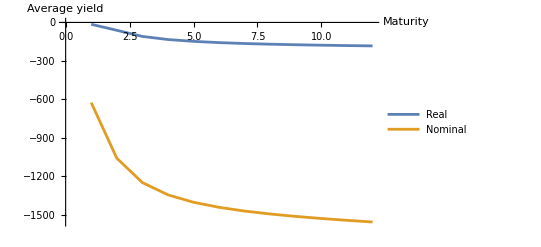

```mathematica
yieldCurve=Table[{m,100*meanYield},{m,1,120}]//toNum[myModel];
nomYieldCurve=Table[{m,100*meanNomYield},{m,1,120}]//toNum[myModel];

ListLinePlot[{yieldCurve,nomYieldCurve},PlotLegends->{"Real","Nominal"},AxesLabel->{"Maturity","Average yield"}]
```

Make an interactive plot:

```mathematica
rhocpRange = {{rhocpM,rhocp/.myModel["params"]},-0.5,0.5};
psiRange =  {{psiM,psi/.myModel["params"]},0.8,2.5};
sol0 = ToNum["Rules",myModel, MaxIterations->500];

Manipulate[
sol=Quiet@ToNum["Rules",myModel,{rhocp->rhocpM, psi->psiM},sol0, MaxIterations->500];
nomYields=Table[{m,100*meanNomYield},{m,1,60}]//.sol;
nomYieldCurve=ListLinePlot[nomYields]
,Evaluate@rhocpRange,Evaluate@psiRange]
```

## Nominal-real covariance

Conditional covariance between nominal bond yields and aggregate market stock returns (stock 1) at different maturities:

```mathematica
nrc=Cov[100*nombondyield[t+1,m],100*ret[t+1,1],t-1,myModel];
```

Plot average "nrc" across maturities:

```mathematica
uncondEnrc=UncondCov[dc[t+m],pi[t],myModel];
```

```mathematica
nrcCurve=Table[{mm,ToNum[uncondEnrc,myModel]/.m->mm},{mm,1,120}]//.sol;
ListLinePlot[nrcCurve,AxesLabel->{"Maturity",Automatic}]
```

$Aborted

-Graphics-

## Variance Ratios for Inflation

The variance ratio for inflation is:

```mathematica
varianceRatio[horizon_,timeAggregation_,model_]:=UncondVar[Growth[pi,t, "numPeriods"->horizon, "TimeAggregation"-> timeAggregation],model]/(horizon*UncondVar[Growth[pi,t, "numPeriods"->1, "TimeAggregation"-> timeAggregation],model])
```

Make a plot of variance ratios at different horizons:

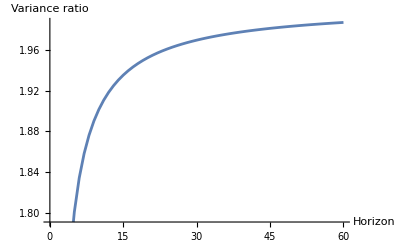

```mathematica
infVR=Table[varianceRatio[h,1,myModel],{h,1,60}]//.myModel["params"];
ListLinePlot[infVR,AxesLabel->{"Horizon","Variance ratio"}]
```

Related Guides

Main Guide

Related Tech Notes

Time Aggregation
Interacting with Models

## Metadata

### Categorization

Tech Note

FernandoDuarte/LongRunRisk

FernandoDuarte`LongRunRisk`

FernandoDuarte/LongRunRisk/tutorial/Workflow

### Keywords

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.